# Medfly Data Analysis

## Functions

```mathematica
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])
GetDataset[experimentsIDs_,dataCorrected_]:=dataCorrected[[#]]&/@experimentsIDs
GetDatasetQuartiles[experimentsIDs_,dataCorrected_]:=Module[{experimentData,lowQuartile,midQuartile,highQuartile},
experimentData=GetDataset[experimentsIDs,dataCorrected];
lowQuartile=((Quantile[#,.25]&/@(experimentData//Transpose))//N);
midQuartile=((Quantile[#,.5]&/@(experimentData//Transpose))//N);
highQuartile=((Quantile[#,.75]&/@(experimentData//Transpose))//N);
{lowQuartile,midQuartile,highQuartile}
]
```

## Probe Experiment

```mathematica
SetDirectory[NotebookDirectory[]]
experimentID=3;
folder="./TwoRelease/";
ρ={3,2,1}//N;
ρ[[experimentID]]
```

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/Datasets/Infertile_WDXX

1.

Males

```mathematica
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
fileNames=FileNames[folder<>"ADM*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[Import[#][[All,2;;All]]&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Define labels and swatches*)
horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}]
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
dataCorrectedM=dataCorrected;
Transpose[{Range[labels//Length],labels}]
```

{{1,1},{1,2},{1,3}}

{{DD_XY,RGBColor[0.293416, 0.0574044, 0.529412]},{WD_XY,RGBColor[0.3361115263157895, 0.13164028421052631, 0.5894257368421052]},{DR_XY,RGBColor[0.378807052631579, 0.2058761684210526, 0.6494394736842105]},{DB_XY,RGBColor[0.4215025789473684, 0.2801120526315789, 0.7094532105263158]},{WW_XY,RGBColor[0.4641981052631579, 0.35434793684210525, 0.769466947368421]},{RW_XY,RGBColor[0.5068936315789474, 0.42858382105263154, 0.8294806842105262]},{BW_XY,RGBColor[0.5495891578947368, 0.5028197052631578, 0.8894944210526315]},{RR_XY,RGBColor[0.5847483684210526, 0.5611895263157894, 0.9099760526315789]},{BR_XY,RGBColor[0.6161394210526315, 0.6116263157894737, 0.9106916315789474]},{BB_XY,RGBColor[0.6475304736842105, 0.6620631052631578, 0.9114072105263158]},{DD_XX,RGBColor[0.6789215263157895, 0.712499894736842, 0.9121227894736842]},{WD_XX,RGBColor[0.7103125789473683, 0.7629366842105263, 0.9128383684210526]},{DR_XX,RGBColor[0.7417036315789474, 0.8133734736842105, 0.9135539473684211]},{DB_XX,RGBColor[0.7720281052631578, 0.8501316842105263, 0.909821105263158]},{WW_XX,RGBColor[0.8002194210526316, 0.8595327368421053, 0.8971914210526316]},{RW_XX,RGBColor[0.8284107368421052, 0.8689337894736842, 0.8845617368421053]},{BW_XX,RGBColor[0.856602052631579, 0.8783348421052631, 0.8719320526315789]},{RR_XX,RGBColor[0.8847933684210526, 0.8877358947368421, 0.8593023684210527]},{BR_XX,RGBColor[0.9129846842105263, 0.897136947368421, 0.8466726842105263]},{BB_XX,RGBColor[0.941176, 0.906538, 0.834043]},{Total,RGBColor[0.25, 0.25, 0.25]}}

{{1,DD_XY},{2,WD_XY},{3,DR_XY},{4,DB_XY},{5,WW_XY},{6,RW_XY},{7,BW_XY},{8,RR_XY},{9,BR_XY},{10,BB_XY},{11,DD_XX},{12,WD_XX},{13,DR_XX},{14,DB_XX},{15,WW_XX},{16,RW_XX},{17,BW_XX},{18,RR_XX},{19,BR_XX},{20,BB_XX},{21,Total}}

```mathematica
{lowQuartile,midQuartile,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrected];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0025],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
males=Show[b,a,c,
PlotRange->All,
Frame->True,
BaseStyle->15,
GridLines->Automatic,
FrameStyle->Thickness[.005],
ImageSize->800,
AspectRatio->1
]
```

-Graphics-

Females

```mathematica
experimentIDindicesA={"0.013"};
experimentIDindicesB={"0.006"};
(*Setup directory and load filenames*)
SetDirectory[NotebookDirectory[]];
fileNames=FileNames[folder<>"AF1*.csv"];
(*Import dataset and detect IDs*)
dataRaw=ParallelMap[Import[#][[All,2;;All]]&,fileNames];
fileNamesIDs=ToExpression/@(StringSplit[#,{"[","|","]"}]&/@fileNames)[[All,2;;4]];
experimentsIDsLabel=fileNamesIDs[[All,1;;2]]//DeleteDuplicates
experimentsIDs=Flatten[Position[fileNamesIDs[[All,1;;2]],#]]&/@experimentsIDsLabel;
(*Define labels and swatches*)
horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}]
(*Reshape datasets for analysis*)
dataCorrected=FixDataEntry[#]&/@dataRaw;
dataCorrectedF=dataCorrected;
(**)
```

{{1,1},{1,2},{1,3}}

{{DD_XY,RGBColor[0.293416, 0.0574044, 0.529412]},{WD_XY,RGBColor[0.3361115263157895, 0.13164028421052631, 0.5894257368421052]},{DR_XY,RGBColor[0.378807052631579, 0.2058761684210526, 0.6494394736842105]},{DB_XY,RGBColor[0.4215025789473684, 0.2801120526315789, 0.7094532105263158]},{WW_XY,RGBColor[0.4641981052631579, 0.35434793684210525, 0.769466947368421]},{RW_XY,RGBColor[0.5068936315789474, 0.42858382105263154, 0.8294806842105262]},{BW_XY,RGBColor[0.5495891578947368, 0.5028197052631578, 0.8894944210526315]},{RR_XY,RGBColor[0.5847483684210526, 0.5611895263157894, 0.9099760526315789]},{BR_XY,RGBColor[0.6161394210526315, 0.6116263157894737, 0.9106916315789474]},{BB_XY,RGBColor[0.6475304736842105, 0.6620631052631578, 0.9114072105263158]},{DD_XX,RGBColor[0.6789215263157895, 0.712499894736842, 0.9121227894736842]},{WD_XX,RGBColor[0.7103125789473683, 0.7629366842105263, 0.9128383684210526]},{DR_XX,RGBColor[0.7417036315789474, 0.8133734736842105, 0.9135539473684211]},{DB_XX,RGBColor[0.7720281052631578, 0.8501316842105263, 0.909821105263158]},{WW_XX,RGBColor[0.8002194210526316, 0.8595327368421053, 0.8971914210526316]},{RW_XX,RGBColor[0.8284107368421052, 0.8689337894736842, 0.8845617368421053]},{BW_XX,RGBColor[0.856602052631579, 0.8783348421052631, 0.8719320526315789]},{RR_XX,RGBColor[0.8847933684210526, 0.8877358947368421, 0.8593023684210527]},{BR_XX,RGBColor[0.9129846842105263, 0.897136947368421, 0.8466726842105263]},{BB_XX,RGBColor[0.941176, 0.906538, 0.834043]},{Total,RGBColor[0.25, 0.25, 0.25]}}

```mathematica
{lowQuartile,midQuartile,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrected];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0025],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.00025],#}&/@colors),PlotRange->All];
females=Show[b,a,c,
PlotRange->All,
Frame->True,
BaseStyle->15,
GridLines->Automatic,
FrameStyle->Thickness[.005],
ImageSize->800,
AspectRatio->1
]
```

-Graphics-

Both

```mathematica
(*tempSwatch=(Reverse[Transpose[swatchPairs]]);
legend=SwatchLegend[tempSwatch[[1]],tempSwatch[[2]],LegendMarkerSize->27,LabelStyle->20,LegendLayout->{"Column",1}];*)
(*Grid[{Style[#,30]&/@{"Females","Males","Combined",""},{females,males,Show[females,males],legend}}]*)
(*Export[Directory[]<>"/MedflyData/MedflySuppression_"<>ToString[ρ[[experimentID]]//Round]<>".jpg",%,ImageSize->5000]*)
```

Total

```mathematica
idFemales={11,12,13,14,15,16,17,18,19,20};
idTotal={21};
idDAllele={1,2,3,4,11,12,13,14};
idRAllele={3,6,8,9,13,16,18,19};
idBAllele={4,9,10,14,17,19,20};
idOfInterest={idFemales,idDAllele,idRAllele,idBAllele,idTotal};
(**)
totalData=dataCorrectedF+dataCorrectedM;
```

```mathematica
genotypeTotals=Table[
Total/@(i//Transpose)
,{i,totalData}]//Transpose;
genotypeMeans=Mean/@genotypeTotals//N
finalMean=Mean[genotypeMeans];
positions=Range[genotypeMeans//Length];(*Position[genotypeMeans,a_/;a>100000];*)

horLength=Length[dataRaw[[1,1]]];
labels=Append[dataRaw[[1]][[1,2;;All]],"Total"][[positions//Flatten]];
colors={Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)]],Black}//Flatten;
colors={ColorData["LakeColors",#]&/@Range[0,1,1/(Length[labels]-2)],Lighter[Black,.25]}//Flatten;
swatchPairs=Transpose[{labels,colors}];
tempSwatch=(Reverse[Transpose[swatchPairs]]);
legend=SwatchLegend[tempSwatch[[1]],tempSwatch[[2]],LegendMarkerSize->27,LabelStyle->20,LegendLayout->{"Column",1}];

{lowQuartile,midQuartile,highQuartile}=Transpose[Transpose[#][[positions//Flatten]]]&/@GetDatasetQuartiles[experimentsIDs[[experimentID]],totalData];

a=ListLinePlot[lowQuartile//Transpose,PlotStyle->({Thickness[.000001],#}&/@colors),PlotRange->All];
b=ListLinePlot[midQuartile//Transpose,PlotStyle->({Thickness[.0075],#}&/@colors),PlotRange->All];
c=ListLinePlot[highQuartile//Transpose,PlotStyle->({Thickness[.0000001],#}&/@colors),PlotRange->All];
females=Grid[{{
pops=Show[b,a,c,
PlotRange->{{250,2500},{0,250000}},
Frame->True,
BaseStyle->20,
GridLines->Automatic,
FrameStyle->Thickness[.0075],
ImageSize->800,
AspectRatio->1,
FrameLabel->(Style[#,30]&/@{"","Population Size"})
],
legend=SwatchLegend[tempSwatch[[1]],tempSwatch[[2]],LegendMarkerSize->27,LabelStyle->20,LegendLayout->{"Column",1}]
}}];
```

{544.817,69127.5,10863.3,420.833,902069.,27212.8,10666.2,124045.,1939.9,316.606,544.328,49161.6,10892.3,415.817,901644.,27233.6,10686.8,124139.,1940.63,298.161,2.27416×10^6}

{5,2}

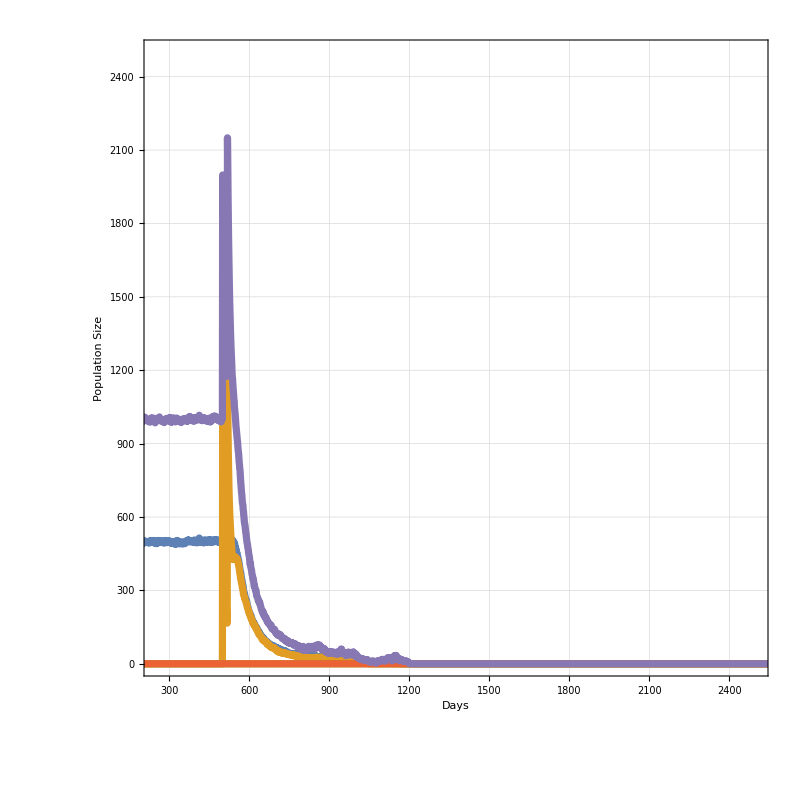
-Graphics- |

/Users/sanchez.hmsc/Documents/GitHub/MedFlyCRISPR-CAS9/Datasets/Infertile_WDXX/TwoRelease_MedflySuppression_1.pdf

```mathematica
Total[(midQuartile//Transpose)[[#]]]&/@idOfInterest;
pops=ListLinePlot[%,
Frame->True,
BaseStyle->17.5,
PlotRange->{{250,2500},{0,2500}},
GridLines->Automatic,
FrameStyle->Directive[Gray,Thickness[.0075]],
ImageSize->800,
AspectRatio->1,
PlotStyle->Thickness[.0065],
FrameLabel->(Style[#,Gray,30]&/@{"Days","Population Size"})
];
labels={"Female","D","R","B","Total"};
legend=SwatchLegend[ColorData[97,"ColorList"][[1;;Length[labels]]],labels,
LegendMarkerSize->30,
LabelStyle->Directive[Gray,20],
LegendLabel->Style["Genotype",30]
];
{lowQuartile,midQuartileF,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrectedF];
{lowQuartile,midQuartileM,highQuartile}=GetDatasetQuartiles[experimentsIDs[[experimentID]],dataCorrectedM];
medianRatios=ReplaceAll[(Last/@midQuartileF)/(Last/@midQuartileM)//Quiet,Indeterminate->0];
ratios=ListLinePlot[medianRatios,
PlotRange->{{250,5000},{0,2}},
Frame->True,
BaseStyle->20,
GridLines->Automatic,
FrameStyle->Directive[Gray,Thickness[.0075]],
ImageSize->800,
AspectRatio->.5,
PlotStyle->Directive[Red,Thickness[.0065]],
FrameLabel->(Style[#,Gray,30]&/@{"Time","(Female/Male) Ratio"})
];
getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];BorderDimensions[im]]
{p1h,p1v}=getPadding[pops];
{p2h,p2v}=getPadding[ratios];
verticalPadding=Max/@Transpose[{p1h,p2h}]
Grid[{{pops,legend}}]
Export[Directory[]<>"/"<>StringSplit[folder,"/"][[2]]<>"_MedflySuppression_"<>ToString[ρ[[experimentID]]//Round]<>".pdf",%,ImageSize->2000]
```